```mathematica
Mac
f = Import["/Users/newlocaluser/Documents/MP2/Data/sData/sofiaNormCrossOmega.mat","LabeledData"];
bciTraits = Import["/Users/newlocaluser/Documents/MP2/Data/David Data/bci.traits.csv"];
species = Import["/Users/newlocaluser/Documents/MP2/Code/species.csv"];
```

Mac

```mathematica
Windows

f=Import["C:/Users/Joel/Documents/CoMPLEX/MP2/sData/sofiaNormCrossOmega.mat","LabeledData"];
bciTraits = Import["C:/Users/Joel/Documents/CoMPLEX/MP2/bci.traits.csv"];
```

Windows

```mathematica
Data Purification
bciAdultNormCrossOmegas10 = Flatten[Values[Select[f,Keys[#]=="bciAdultNormCrossOmegas10"&]],1];
index14110 = Flatten[Values[Select[f,Keys[#]=="index141_10"&]]];
clusterIndices = Map[IntegerPart[#]&,Flatten[Values[Select[f,Keys[#]=="bciAdultClusterIndices10_5_141"&]]]];
B=MapThread[If[#2,MapThread[If[#2,#1,0]&,{#1,index14110}],ConstantArray[0,Length[#1]]]&,{bciAdultNormCrossOmegas10,index14110}];
clusterSpecies = DeleteCases[Flatten[MapIndexed[If[Length[DeleteCases[#,0]]>0,#2,0]&,B]],0];
clusters = Map[Keys[#]&,GatherBy[MapThread[#1->#2&,{clusterSpecies,clusterIndices}],Values[#]&]];
speciesMap = MapThread[#1->First[#2]&,{clusterSpecies,species}];
bciTraits[[2;;All,2]];
bciValid = Flatten[Select[MapIndexed[With[{name=First[#1],index=First[#2]},index->Flatten[Select[bciTraits,MemberQ[#,name]&],1]]&,species],Values[#]≠{}&],1];
```

Data Purification

```mathematica
Graph Construction

Manipulate[
A = DeleteDuplicates[DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1>adjacencyThreshold && i≠j,i->j,0]]&,#1]]&,B]],0]];
W = DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1>adjacencyThreshold && i≠j,#1,0]]&,#1]]&,B]],0];

An = DeleteDuplicates[DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1<-adjacencyThreshold && i≠j,i->j,0]]&,#1]]&,B]],0]];
Wn = DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1< -adjacencyThreshold && i≠j,#1,0]]&,#1]]&,B]],0];
validSpecies = DeleteDuplicates[Map[Keys[#]&,A]];
validClusters = Map[Intersection[#,validSpecies]&,clusters];
gn = Graph[An,DirectedEdges->True,EdgeWeight->Abs[Wn]];
gp =Graph[A,DirectedEdges->True,EdgeWeight->W];
g = Graph[Join[An,A],DirectedEdges->True,EdgeWeight->Join[Wn,W]];
{gp,gn,g}

,{adjacencyThreshold,2.75},ControlType->InputField]
```

Construction Graph

Anton

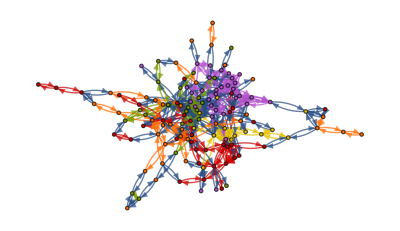

-Graphics-

{{5,10,11,18,25,39,43,45,63,90,92,93,107,112,114,121,125,127,137},{3,48,74,110,116},{6,7,17,40,46,58,69,70,131,132,140,141},{9,19,34,36,44,55,59,64,72,78,79,91,104,119},{32,57,71,83,118,124}}

```mathematica
Anton

HighlightGraph[g,Map[Subgraph[g,#]&,validClusters]]
CommunityGraphPlot[g,validClusters]
antonSpeciesClusters =Map[Intersection[Keys[bciValid],#]&,validClusters]
```

# Social Network Analysis

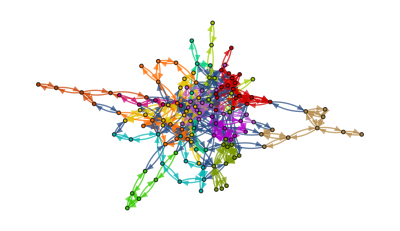

-Graphics-

{{6,7,17,46,58,69,70,118,140,141},{25,36,39,71,90,92,107,124,137},{19,57,63,91},{10,18,32,72,93},{11,40,45,114,121,127},{9,34,44,64,74,116},{112},{3,119,132},{48},{5,110,131},{43,59,78,79},{83,104},{55,125}}

```mathematica
communities = FindGraphCommunities[gp,Method->"Modularity"];
HighlightGraph[g,Map[Subgraph[g,#]&,communities]]
CommunityGraphPlot[g,communities]
snSpeciesClusters =Map[Intersection[Keys[bciValid],#]&,communities]
```

```mathematica
ValidData[var_] := Not[MemberQ[Map[NumberQ[#]&,var],False]]
```

```mathematica
Trait Space
```

```mathematica
bciNonNullValues = DeleteCases[Map[If[ValidData[Take[#,-3]],Take[#,{6,25}],Invalid]&,Values[bciValid]],Invalid];
bciNonNullKeys = DeleteCases[Map[If[ValidData[Take[Values[#],-3]],Keys[#],Invalid]&,bciValid],Invalid];
```

```mathematica
reducedData = MapThread[#2->#1&,{ DimensionReduce[bciNonNullValues,3],bciNonNullKeys}];
antonClusteredReducedData = DeleteCases[Map[DeleteCases[Map[Lookup[reducedData,#,Missing]&,#],Missing]&,antonSpeciesClusters],{}];
snClusteredReducedData = DeleteCases[Map[DeleteCases[Map[Lookup[reducedData,#,Missing]&,#],Missing]&,snSpeciesClusters],{}];
```

```mathematica
{Anton->ListPointPlot3D[antonClusteredReducedData,Axes->True],SN->ListPointPlot3D[snClusteredReducedData,Axes->True]}
```

{Anton→-Graphics3D-,SN→-Graphics3D-}